```mathematica
(*Initialization*)
ClearAll["Global`*"];

(*Constants*)

NBar=10^4;(*Mean droplet size*)
r=0.9;(*Ratio of standard deviation to the mean*)

(*Log-normal distribution parameters*)
mu=Log[NBar/Sqrt[1+r^2]];
delta=Sqrt[Log[1+r^2]];

(*Function Definitions*)

(*Size[n]:Log-normal probability distribution for droplet size*)
Size[n_]:=1/(n*delta*Sqrt[2*Pi])*Exp[-(Log[n]-mu)^2/(2*delta^2)];

(*KWithSize[n,a]:Poisson probability for dopant pickup given size n and dopant rate a*)
KWithSize[n_,a_]:=a*n^(2/3)*Exp[-a*n^(2/3)];

(*Calculations*)
(*Compute probability K,expected size AvSize,and expected size given monomer AvSizeWithK*)
(*Results are stored as {aValue,K,AvSize,AvSizeWithK}*)
CalculateValues[aValue_]:=Module[{K,AvSize,AvSizeWithK},K=NIntegrate[Size[n]*KWithSize[n,aValue],{n,0,Infinity}];
AvSize=NIntegrate[n*Size[n],{n,0,Infinity}];
AvSizeWithK=NIntegrate[n*Size[n]*KWithSize[n,aValue]/K,{n,0,Infinity}];
{aValue,K,AvSize,AvSizeWithK}];

(*Interactive visualization*)
Manipulate[Module[{values,plot},values=CalculateValues[a];
plot=ListPlot[{{a,NBar-values[[4]]}},PlotRange->{{0,0.02},{-4000,10000}},AxesOrigin->{0,0},AxesLabel->{"a","Deviation from <N>"},PlotMarkers->{Automatic,10},PlotStyle->Red,PlotLabel->Style["Deviation of Average Monomer-Containing Droplet Size",Bold],ImageSize->Medium,LabelStyle->{Black,Bold,14}];
(*Output the plot and calculated values*){plot,"For a = "<>ToString[a],"K = "<>ToString[values[[2]]],"<N> - AvSizeWithK = "<>ToString[NBar-values[[4]]]}],{{a,0.001,"Dopant Rate a"},3*10^-4,2*10^-2,1.7*10^-3,Appearance->"Labeled"}]
```

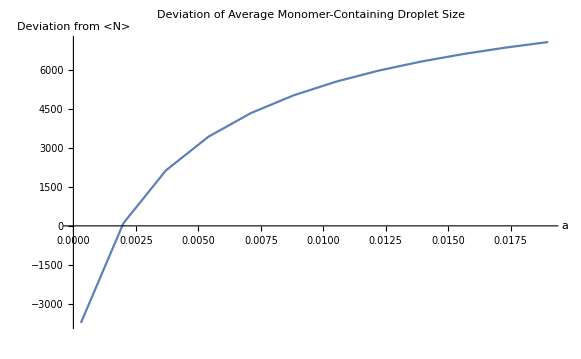

```mathematica
(*Define the constants*)
NBar=10^4;(*Mean droplet size*)
r=0.9;(*Ratio of the standard deviation to the mean*)
mu=Log[NBar/Sqrt[1+r^2]];(*First moment,equivalent to the mean in log space*)
delta=Sqrt[Log[1+r^2]];(*Standard deviation in log space*)
aValues=Range[3*10^-4,2*10^-2,1.7*10^-3];(*Sequence of a values*)

(*Function to calculate the probability Size[n] for a given droplet size n*)
Size[n_]:=1/(n*delta*Sqrt[2*Pi])*Exp[-(Log[n]-mu)^2/(2*delta^2)];

(*Function to calculate the Poisson probability KWithSize[n] for a given droplet size n and dopant rate a*)
KWithSize[n_,a_]:=a*n^(2/3)*Exp[-a*n^(2/3)];

(*Initialize lists to hold results*)
avSizeWithKList={};
kList={};

(*Calculate for each a value*)
Do[(*Calculate the absolute probability K that the droplet contains a monomer*)K=NIntegrate[Size[n]*KWithSize[n,a],{n,0,Infinity}];
(*Calculate the expected value of the droplet size*)AvSize=NIntegrate[n*Size[n],{n,0,Infinity}];
(*Calculate the expected value of droplet size given that it contains a monomer*)AvSizeWithK=NIntegrate[n*Size[n]*KWithSize[n,a]/K,{n,0,Infinity}];
(*Append results to the lists*)AppendTo[avSizeWithKList,AvSizeWithK];
AppendTo[kList,K];,{a,aValues}];

(*Plot the deviation of average monomer-containing droplet size from<N>as a function of a*)
deviationPlot=ListPlot[Transpose[{aValues,NBar-avSizeWithKList}],Joined->True,PlotRange->All,AxesLabel->{"a","Deviation from <N>"},PlotLabel->"Deviation of Average Monomer-Containing Droplet Size"]
```

```mathematica
(*Constants*)r=0.9;
NBar=10^4;
mu=Log[NBar/Sqrt[1+r^2]];
delta=Sqrt[Log[1+r^2]];

(*Functions*)
Size[n_]:=1/(n*delta*Sqrt[2*Pi])*Exp[-1/2 ((Log[n]-mu)/delta)^2];
KWithSize[n_,a_]:=a*n^(2/3)*Exp[-a*n^(2/3)];
SizeWithK[n_,a_,K_]:=(Size[n]*KWithSize[n,a])/K;
```

```mathematica
Manipulate[Plot[KWithSize[n,a],{n,0,50000},PlotLabel->"Probability of monomer pickup given droplet is size n",AxesLabel->{"droplet size","P"}],{{a,3*10^-4,"Value of a"},3*10^-4,2*10^-2,1.7*10^-3,Appearance->"Labeled"}]
```

```mathematica
Manipulate[K=NIntegrate[Size[n]*KWithSize[n,a],{n,0,Infinity},MaxRecursion->50,PrecisionGoal->3];
Plot[SizeWithK[n,a,K],{n,0,50000},PlotRange->{{0,50000},{0,0.0002}},PlotLabel->"Probability of droplet size n given monomer pickup",AxesLabel->{"droplet size","P"}],{{a,3*10^-4,"Value of a"},3*10^-4,2*10^-2,1*10^-4,Appearance->"Labeled"}]
```

```mathematica
Manipulate[K=NIntegrate[Size[n]*KWithSize[n,a],{n,0,Infinity},MaxRecursion->50,PrecisionGoal->3];
plot=Plot[SizeWithK[n,a,K],{n,0,50000},PlotRange->{{0,50000},{0,0.0002}},PlotLabel->"Probability of droplet size N given monomer pickup",AxesLabel->{"droplet size","P"}],{{a,3*10^-4,"Value of a"},3*10^-4,2*10^-2,1.7*10^-3,Appearance->"Labeled"}]
```